```mathematica
ClearAll["Global`*"];

ClearAll[baseTerm,SolveTruncatedSystemDirect];
baseTerm[r_Integer?Positive]:=(1-(-1)^r)/(Pi^2 r);


SolveTruncatedSystemDirect[M_Integer?Positive,J_?NumericQ,gamma_?NumericQ]:=
Module[
{rVals=Range[M],fMat,A,rhs,b},
fMat=Table[
   If[n==r,(32.0 J^2 r^2)/(1-4 r^2),
If[EvenQ[n+r],(32.0 J^2 n r)/(n^4-2 n^2 (r^2+1)+(r^2-1)^2),0.]],
   {n,1,M},{r,1,M}];

A=Table[If[r==n,gamma rVals[[r]] Pi J,0.]-fMat[[n,r]],{r,1,M},{n,1,M}];

rhs=Table[gamma rVals[[r]] Pi J baseTerm[rVals[[r]]],{r,1,M}];

Print["Dimensions[A] = ",Dimensions[A],", Length[rhs] = ",Length[rhs]];

b=LinearSolve[A,rhs];
{rVals,b}];
```

```mathematica
(* Parameters*)
M=800;
J=1.0;
gamma=1.0;
(* check solve truncated system direct *)
sol=SolveTruncatedSystemDirect[M,J,gamma];
{rVals,bVals}=sol;
```

Dimensions[A] = {800,800}, Length[rhs] = 800

```mathematica
(*Building Blocks*)
ClearAll[stepTheta];

stepTheta[x_?NumericQ]:=Which[x>0,1.,x<0,0.,True,0.5];

nL[_?NumericQ] := 0.;
nR[_?NumericQ] := 1/(2. Pi);

ChiPlus[k_?NumericQ, rVals_List, bVals_List] := 
	stepTheta[k] (bVals . Sin[rVals k] ) + stepTheta[-k](nR[k] + bVals . Sin[rVals k]);

nZeta[k_?NumericQ, zeta_?NumericQ, rVals_List, bVals_List] :=
	Module[{epsp, chi},
	epsp = 2. Sin[k];
	chi = ChiPlus[k, rVals, bVals];
	If[k>0,
	stepTheta[-zeta] nL[k] + stepTheta[zeta] stepTheta[epsp-zeta] chi + stepTheta[zeta- epsp]nR[k],
                stepTheta[zeta] nR[k] + stepTheta[-zeta] stepTheta[-epsp+ zeta] chi + stepTheta[ epsp -zeta] nL[k]
]	
];
(* Charges*)
qPlus[k_?NumericQ, r_Integer?NonNegative] := 2. Cos[r k];
qMinus[k_?NumericQ, r_Integer?NonNegative] := -2. Sin[r k];

(*2) Quick sanity check of ingredients (uses rVals,bVals from your solver)*)
k0=0.7;z0=0.2;
{stepTheta[k0],nL[k0],nR[k0],ChiPlus[k0,rVals,bVals],nZeta[k0,z0,rVals,bVals]}
```

{1.,0.,0.159155,0.050237,0.050237}

```mathematica
(*Integrands*)

chargeIntegrand[k_?NumericQ, r_Integer?NonNegative, zeta_?NumericQ, sign_String,  rVals_List, bVals_List]:=
	If[ sign === "-", qMinus[k,r], qPlus[k,r]]*nZeta [k, zeta, rVals, bVals];

currentIntegrand[ k_?NumericQ, r_Integer?NonNegative, zeta_?NumericQ, sign_String, rVals_List, bVals_List] :=
	2. Sin[k] * If[ sign=== "-",  qMinus[k,r], qPlus[k,r]] * nZeta[k, zeta, rVals, bVals];


(*4) Single-point q,J check*)
rTest=1;signTest="-";zTest=-0.01;

qTest=NIntegrate[chargeIntegrand[k,rTest,zTest,signTest,rVals,bVals],{k,-Pi,Pi},Method->{"GlobalAdaptive","SymbolicProcessing"->0},MinRecursion->3,MaxRecursion->30,AccuracyGoal->8,PrecisionGoal->8];

JTest=NIntegrate[currentIntegrand[k,rTest,zTest,signTest,rVals,bVals],{k,-Pi,Pi},Method->{"GlobalAdaptive","SymbolicProcessing"->0},MinRecursion->3,MaxRecursion->30,AccuracyGoal->8,PrecisionGoal->10];

{qTest, JTest}
```

{0.464308,-0.767846}

```mathematica
(* 5) zeta scan with checks  *)

zStep=10;
zetas=Subdivide[-3,3,zStep];

qVals= Table[
	NIntegrate[chargeIntegrand[k, rTest, z, signTest, rVals, bVals], {k, -Pi, Pi}, Method -> {"GlobalAdaptive", "SymbolicProcessing"->0},
       MinRecursion->3, MaxRecursion-> 30,AccuracyGoal-> 10, PrecisionGoal-> 8] , {z,zetas}];

JVals =  Table[
		NIntegrate[ currentIntegrand[k, rTest, z, signTest, rVals, bVals], {k, -Pi, Pi }, Method->{"GlobalAdaptive", "SymbolicProcessing"->0},
	      MinRecursion->3, MaxRecursion->30,AccuracyGoal->10, PrecisionGoal->8], {z,zetas}];

{VectorQ[qVals,NumericQ],VectorQ[JVals,NumericQ],MinMax[qVals],MinMax[JVals]}
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{True,True,{-2.77556×10^-17,0.464307},{-2.,0.}}

```mathematica
(*6) Plot and Save test *)
plot=ListLinePlot[
{Transpose[{zetas,qVals}], Transpose[{zetas, JVals} ] },
    PlotLegends->{"q", "J"},
	Frame->True,
	FrameLabel->{"zeta","value"},
	  ImageSize->600
];
data= Transpose[{zetas, qVals, JVals}];
fileStem = StringTemplate["GHD_vac_fill_r``_sign``_M``_gamma``"][rTest, signTest, M, gamma];

outBase=FileNameJoin[{NotebookDirectory[],"GHD_vac_fill_mat"}];
csvDir=FileNameJoin[{outBase,"csv"}];
pngDir=FileNameJoin[{outBase,"png"}];

csvOut = FileNameJoin[{csvDir, fileStem<>".csv"}];
pngOut = FileNameJoin[{pngDir, fileStem<>".png"}];

Export[csvOut, Prepend[data,{"zeta", "q", "J"}], "CSV"];
Export[pngOut, plot,"PNG" ];

Print["Saved CSV:", csvOut];
Print["Saved PMG:", pngOut]
```

Saved CSV:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/csv/GHD_vac_fill_r1_sign-_M800_gamma1.0.csv

Saved PMG:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/png/GHD_vac_fill_r1_sign-_M800_gamma1.0.png

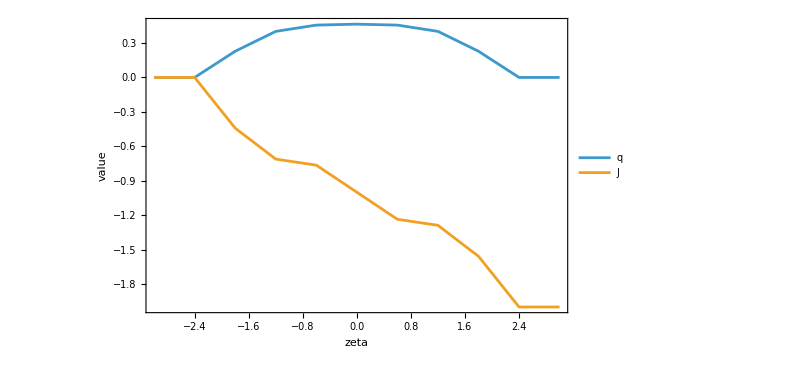

```mathematica
%797
```

```mathematica
(*8)  Nonuniform zeta grid + loop over even/odd r*)

Mval= 800;
Jval= 1.0;
gammaval = 1.0; 

{RVals, BVals} = SolveTruncatedSystemDirect[Mval, Jval, gammaval];
(* grid  *)

zetasVal= Join[
Subdivide[-2.5,-1., 60],
Rest @Subdivide[-1., 1., 270],
Rest@Subdivide[1., 2.5, 60]
];
(* even r with +, odd r with -*)
profileList = Join[
	Table[{r,"-"}, {r, {1, 3, 5} }],
	Table[{r,"+"}, {r, {0,2,4} }]
];


Do[
{rval, signval} =rs;
Print["Running r=", rval, " sign=", signval];

qV= Table[
NIntegrate[
chargeIntegrand[k, rval, z, signval, RVals, BVals],
{k,-Pi, Pi},
Method->{"GlobalAdaptive","SymbolicProcessing"->0},
MinRecursion->3,MaxRecursion->30,
AccuracyGoal->10,PrecisionGoal->8
],
{z,zetasVal} 
];

JV= Table[
NIntegrate[
currentIntegrand[k, rval, z, signval, RVals, BVals],
{k,-Pi, Pi},
Method->{"GlobalAdaptive","SymbolicProcessing"->0},
MinRecursion->3,MaxRecursion->30,
AccuracyGoal->10,PrecisionGoal->8
],
{z,zetasVal} 
];

dataV= Transpose[{zetasVal, qV, JV}];

plot = ListLinePlot[
{Transpose[{zetasVal,qV}],Transpose[{zetasVal,JV}]},
PlotLegends->{"q","J"},
Frame->True,
FrameLabel->{"zeta","value"},
PlotLabel->Row[{"vac-fill, r=",rval,", sign=",signval,", M=",Mval,", gamma=",gammaval}],ImageSize->700
];

     gammaTag= StringReplace[
ToString @ NumberForm[N[gammaval], {Infinity, 2}, NumberPadding->{" ", "0"} ],
" "-> ""
];

fileST=StringTemplate["GHD_vac_fill_r``_sign``_M``_gamma``_seggrid"][rval,signval,Mval,gammaval];
     csvOut=FileNameJoin[{csvDir,fileST<>".csv"}];
     pngOut=FileNameJoin[{pngDir,fileST<>".png"}];

Export[csvOut, Prepend[ dataV, {"zeta", "q", "J"}], "CSV"];
Export[pngOut, plot, "PNG"];
Print["Saved CSV:", csvOut];
Print["Saved PMG:", pngOut]

, {rs, profileList} ];
```

Dimensions[A] = {800,800}, Length[rhs] = 800

Running r=1 sign=-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NumberForm::iprf: Formatting specification {∞,2} should be a positive integer or a pair of positive integers.

Saved CSV:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/csv/GHD_vac_fill_r1_sign-_M800_gamma1.0_seggrid.csv

Saved PMG:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/png/GHD_vac_fill_r1_sign-_M800_gamma1.0_seggrid.png

Running r=3 sign=-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in k near {k} = {-2.55923}. NIntegrate obtained -0.0527972 and 5.76781×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in k near {k} = {-2.58888}. NIntegrate obtained -0.0413052 and 5.8112×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in k near {k} = {-2.6035}. NIntegrate obtained -0.0357249 and 6.45471×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NumberForm::iprf: Formatting specification {∞,2} should be a positive integer or a pair of positive integers.

Saved CSV:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/csv/GHD_vac_fill_r3_sign-_M800_gamma1.0_seggrid.csv

Saved PMG:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/png/GHD_vac_fill_r3_sign-_M800_gamma1.0_seggrid.png

Running r=5 sign=-

NumberForm::iprf: Formatting specification {∞,2} should be a positive integer or a pair of positive integers.

General::stop: Further output of NumberForm::iprf will be suppressed during this calculation.

Saved CSV:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/csv/GHD_vac_fill_r5_sign-_M800_gamma1.0_seggrid.csv

Saved PMG:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/png/GHD_vac_fill_r5_sign-_M800_gamma1.0_seggrid.png

Running r=0 sign=+

Saved CSV:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/csv/GHD_vac_fill_r0_sign+_M800_gamma1.0_seggrid.csv

Saved PMG:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/png/GHD_vac_fill_r0_sign+_M800_gamma1.0_seggrid.png

Running r=2 sign=+

Saved CSV:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/csv/GHD_vac_fill_r2_sign+_M800_gamma1.0_seggrid.csv

Saved PMG:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/png/GHD_vac_fill_r2_sign+_M800_gamma1.0_seggrid.png

Running r=4 sign=+

Saved CSV:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/csv/GHD_vac_fill_r4_sign+_M800_gamma1.0_seggrid.csv

Saved PMG:/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_vac_fill_mat/png/GHD_vac_fill_r4_sign+_M800_gamma1.0_seggrid.png